# Chapter 1: Numerical Solution Problems

## AER 4074 - ORBITAL Mechanics By: Mohammad Khalid Gamal Ali | Sec:2, BN:14

## Problem 1.18:

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
sol18=NDSolve[{y''''[t]+2y''[t]+y[t]==0,y[0]==1,y'[0]==0,y''[0]==0,y'''[0]==0},y,{t,0,20}];
```

```mathematica
Evaluate[y[20]/.sol18]
```

{9.53753}

## Problem 1.19:

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
sol19=NDSolve[{y'''[t]+3y''[t]-4y'[t]-12y[t]==t*N[E]^(2*t),y[0]==0,y'[0]==0,y''[0]==0},y,{t,0,20}];
```

```mathematica
Evaluate[y[3]/.sol19]
```

{66.6161}

## Problem 1.20:

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
sol20=NDSolve[{t*y''[t]+t^2 y'[t]-2y[t]==0,y[1]==0,y'[1]==1},y,{t,1,4}];
```

```mathematica
Evaluate[y[4]/.sol20]
```

{1.28873}

## Problem 1.21:

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
sol21=NDSolve[{x'[t]+0.5y[t]-z[t]==0,-.5x[t]+y'[t]+1/Sqrt[2] z[t]==0,1/2 x[t]-1/Sqrt[2] y[t]+z'[t]==0,x[0]==1,y[0]==0,z[0]==0},{x,y,z},{t,0,30}];
```

```mathematica
Evaluate[x[20]/.sol21]
Evaluate[y[20]/.sol21]
Evaluate[z[20]/.sol21]
```

{6.30318}

{5.26643}

{3.62172}

## Problem 1.22:

{1.10089×10^8}

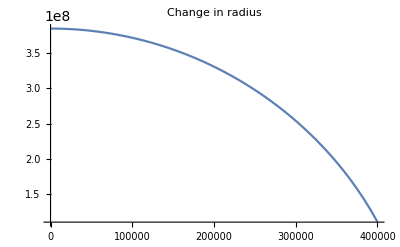

```mathematica
ClearAll["Global`*"]
Subscript[M, E]=5.972×10^24;
G=6.674*10^-11;
Subscript[R, E]=6371000;
Subscript[r, m]=1737000;
sol=NDSolve[{r1'[t]==r2[t],r2'[t]==(-G*Subscript[M, E])/(Subscript[R, E]+Subscript[r, m]+r1[t])^2,r1[0]==385000000,r2[0]==0},{r1,r2},{t,0,400000},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
r=Evaluate[r1[400000]/.sol]
Plot[Evaluate[r1[t]/.sol],{t,0,400000},PlotLabel->"Change in radius"]
```

## Problem 1.23:

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
σ=10;
β=8/3;
ρ=28;
```

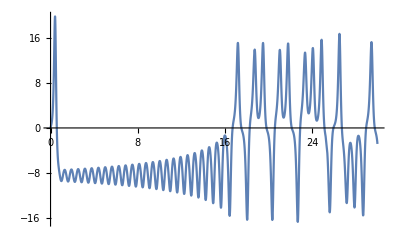

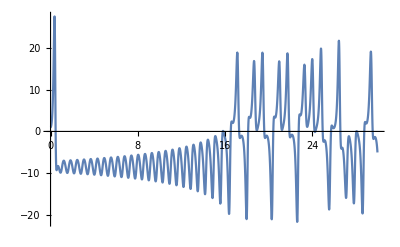

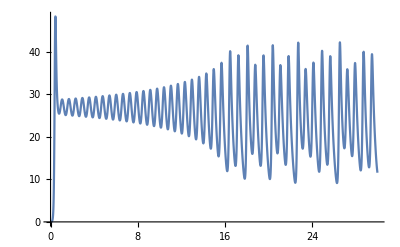

-Graphics3D-

```mathematica
sol23=
NDSolve[{x'[t]==σ*(y[t]-x[t]),y'[t]==x[t]*(ρ-z[t])-y[t],z'[t]==x[t]*y[t]-β*z[t],x[0]==0,y[0]==1,z[0]==0},{x,y,z},{t,0,30},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
X=Evaluate[x[t]/.sol23];
Y=Evaluate[y[t]/.sol23];
Z=Evaluate[z[t]/.sol23];
xx=Plot[X,{t,0,30}]
yy=Plot[Y,{t,0,30}]
zz=Plot[Z,{t,0,30}]
ParametricPlot3D[{x[t],y[t],z[t]}/.sol23,{t,0,30},PlotRange->All]
```